```mathematica
path="G:\\GitHub Local Repository\\Mathematical-Modeling-Campus-Competition";
```

# 数学建模

导入数据

```mathematica
data=Import["G:\\GitHub Local Repository\\Mathematical-Modeling-Campus-Competition\\2020年兰州大学数学建模竞赛赛题 (1)\\Data.xlsx"];
```

```mathematica
data//Dimensions
```

{2}

```mathematica
train=data[[1,2;;All]];
```

```mathematica
test=data[[2,2;;All]];
```

数据预处理

```mathematica
asso=MapThread[Rule,{train[[All,1;;7]],train[[All,8]]}][[2;;All]];
```

```mathematica
model=Classify[asso,Method->"SupportVectorMachine"];
```

## 探索 7指标分类器

```mathematica
Information[model]
```

Classifier information
Data type | NumericalVector (length: 7)
Classes | ,,0.1.
Accuracy | (91.80.8) %
Method | SupportVectorMachine
Single evaluation time | 6.66 ms/example
Batch evaluation speed | 5.12 examples/ms
Loss | 0.257 ± 0.014
Model memory | 1.21 MB
Training examples used | 19999 examples
Training time | 1 32
 |

```mathematica
model[test[[2]]]
```

1.

## 进行主成分分析

```mathematica
features=train[[All,1;;7]];
```

```mathematica
lables=train[[All,8]];
```

得到降维后的数据

```mathematica
reduced=(KarhunenLoeveDecomposition[Transpose[features]][[1]]//Transpose)[[All,1;;2]];
```

现在要求出主向量

```mathematica
{b,m}=KarhunenLoeveDecomposition[Transpose[features],Standardized->False];
```

对降维后的数据进行画图操作：

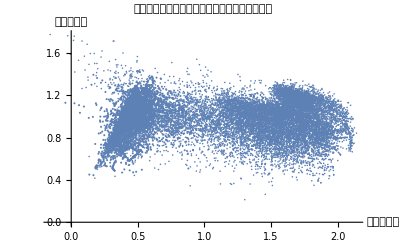

```mathematica
Show[ListPlot@point1,ListPlot@point2,AxesLabel->{"第一主成分","第二主成分"},PlotLabel->"训练集在两个最主成分构成的特征空间中的分布"]
```

```mathematica
path="G:\\GitHub Local Repository\\Mathematical-Modeling-Campus-Competition";
```

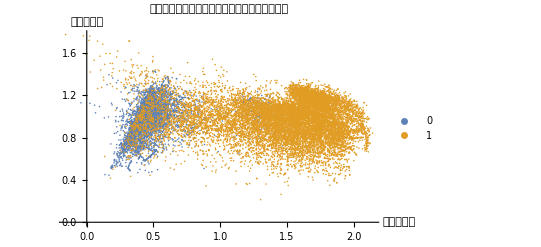
```mathematica
Export[path<>"\\训练集在两个最主成分构成的特征空间中的分布图（有色）.jpg",-Graphics-];
```

```mathematica
po1=Position[lables,x_/;x==1]//Flatten;
```

```mathematica
po2=Position[lables,x_/;x==0]//Flatten;
```

```mathematica
point1=reduced[[po1]];
```

```mathematica
point2=reduced[[po2]];
```

```mathematica
point1//Dimensions
```

{13895,2}

```mathematica
ListPlot[{point2,point1},PlotRange->{Full,All},AxesLabel->{"第一主成分","第二主成分"},PlotLabel->"训练集在两个最主成分构成的特征空间中的分布",PlotLegends->{0,1}]
```

-Graphics-

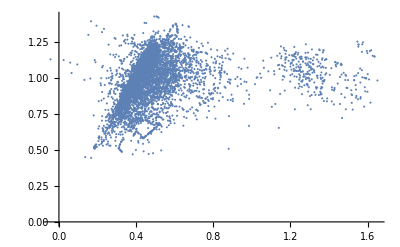

```mathematica
ListPlot[{point2},PlotRange->{Full,All}]
```

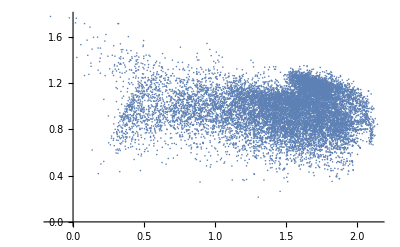

```mathematica
ListPlot[{point1},PlotRange->{Full,All}]
```

我们来探究一下主成分分析的合理性，首先我们求取协方差矩阵。

```mathematica
Covariance[features]//MatrixForm//TeXForm
```

\left(
\begin{array}{ccccccc}
 0.0985186 & 0.0943964 & 0.0853236 & 0.0304429 & 0.0527863 & 0.0124883 & 0.014629 \\
 0.0943964 & 0.109691 & 0.0843306 & 0.0344634 & 0.0559192 & 0.0162319 & 0.0191176 \\
 0.0853236 & 0.0843306 & 0.0849893 & 0.0273838 & 0.0516196 & 0.0112965 & 0.0144296 \\
 0.0304429 & 0.0344634 & 0.0273838 & 0.0172714 & 0.0219271 & 0.0109203 & 0.00977298 \\
 0.0527863 & 0.0559192 & 0.0516196 & 0.0219271 & 0.0443377 & 0.0141748 & 0.017051 \\
 0.0124883 & 0.0162319 & 0.0112965 & 0.0109203 & 0.0141748 & 0.015963 & 0.011729 \\
 0.014629 & 0.0191176 & 0.0144296 & 0.00977298 & 0.017051 & 0.011729 & 0.0153588 \\
\end{array}
\right)

```mathematica
eig=Covariance[features]//Eigenvalues;
```

```mathematica
eig/Total[eig]//TeXForm
```

\{0.840721,0.0756435,0.0358832,0.018512,0.0117046,0.0113928,0.00614299\}

```mathematica
Accumulate[eig]/Total[eig]//TeXForm
```

\{0.840721,0.916364,0.952248,0.97076,0.982464,0.993857,1.\}

## 定义计算

```mathematica
count[x_,y_][r_,point_]:=(If[(x-r)<#[[1]]<(x+r)&&(y-r)<#[[2]]<(y+r),1,0]&/@point//Total)
```

衬比度

```mathematica
Obvious[x_,y_]:=If[
x≠0||y≠0,Abs@(x-y)/(x+y),0.3
]//N
```

```mathematica
p[r_,h_,point_]:=ParallelTable[{x,y,count[x,y][r,point]},{x,0,2.5,h},{y,0,2,h}];
```

```mathematica
list[r_,h_]:=MapThread[{#1[[1]],#1[[2]],Obvious[#1[[3]],#2[[3]]]}&,{p[r,h,point1],p[r,h,point2]},2];
```

```mathematica
contour=Flatten[list[0.05,0.1],1];
```

```mathematica
contour//Dimensions
```

{546,3}

```mathematica
Select[contour,(#[[3]]<0.18)&]
```

{{0.2,0.4,0.},{0.2,1.3,0.},{0.4,1.3,0.0833333},{0.6,0.8,0.0181818},{0.7,1.,0.101695},{0.7,1.1,0.165049},{0.7,1.4,0.}}

```mathematica
var1=m[[1]].variables
```

0.532456 V1+0.558647 V2+0.489608 V3+0.189288 V4+0.328206 V5+0.0947973 V6+0.110235 V7

```mathematica
var2=m[[2]].variables
```

-0.302602 V1-0.0318648 V2-0.223899 V3+0.278935 V4+0.364256 V5+0.589206 V6+0.547389 V7

```mathematica
{{#[[1]]-0.05<var1<#[[1]]+0.05},{#[[2]]-0.05<var2<#[[2]]+0.05}}&[{0.2,0.4,0.}]//Column//TeXForm
```

\begin{array}{l}
 \{0.15<0.532456 \text{V1}+0.558647 \text{V2}+0.489608 \text{V3}+0.189288 \text{V4}+0.328206 \text{V5}+0.0947973
   \text{V6}+0.110235 \text{V7}<0.25\} \\
 \{0.35<-0.302602 \text{V1}-0.0318648 \text{V2}-0.223899 \text{V3}+0.278935 \text{V4}+0.364256 \text{V5}+0.589206
   \text{V6}+0.547389 \text{V7}<0.45\} \\
\end{array}

```mathematica
variables={V1,V2,V3,V4,V5,V6,V7};
```

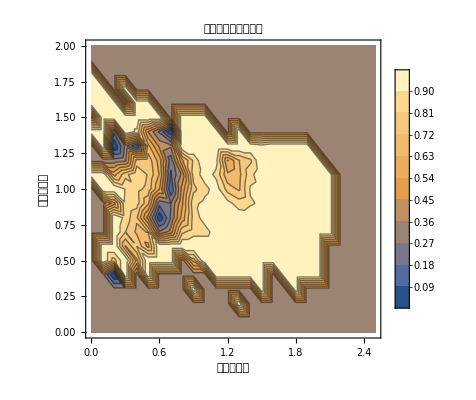

```mathematica
con=ListContourPlot[contour,PlotLegends->Automatic,Contours->10,PlotLabel->"明显度函数的等高图",FrameLabel->{"第一主特征","第二主特征"}]
```

```mathematica
Export[path<>"//点集与明显度函数对比.jpg",show];
```

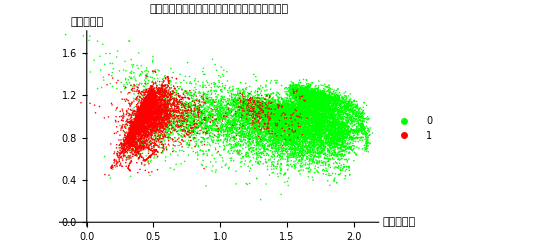

```mathematica
lis=ListPlot[{point1,point2},PlotStyle->{Green,Red},AxesLabel->{"第一主成分","第二主成分"},PlotLabel->"训练集在两个最主成分构成的特征空间中的分布",PlotLegends->{0,1}]
```

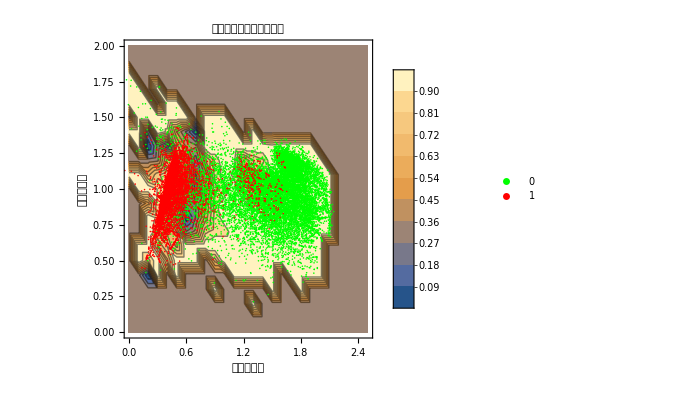

```mathematica
show=Show[con,lis,PlotLabel->"点集与明显度函数对比图"]
```

## 给出模糊区域的数学表达式

我们取0.18作为阈值

```mathematica
Select[]
```

## 对测试集进行降维

```mathematica
transformedtest=Transpose[m.Transpose[test]][[All,1;;2]];
```

```mathematica
transformedtest//Dimensions
```

{5000,2}

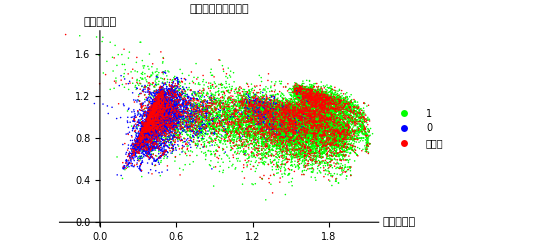

```mathematica
compare=ListPlot[{point1,point2,transformedtest},PlotStyle->{Green,Blue,Red},PlotLegends->{1,0,"测试集"},PlotLabel->"训练集和测试集对比",AxesLabel->{"第一主向量","第二主向量"}]
```

```mathematica
Export[path<>"\\训练集和测试集的对比.jpg",compare];
```

```mathematica
asso2=MapThread[Rule,{reduced,lables}];
```

## 线性核

```mathematica
model2=Classify[asso2,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
```

```mathematica
model2//Information
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,0.1.
Accuracy | (91.21.3) %
Method | SupportVectorMachine
Single evaluation time | 4.51 ms/example
Batch evaluation speed | 11.9 examples/ms
Loss | 0.256 ± 0.039
Model memory | 1.02 MB
Training examples used | 20000 examples
Training time | 52.3 s
 |

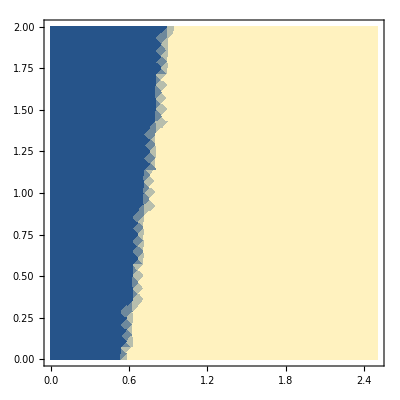

```mathematica
dens=DensityPlot[model2[{x,y}],{x,0,2.5},{y,0,2}]
```

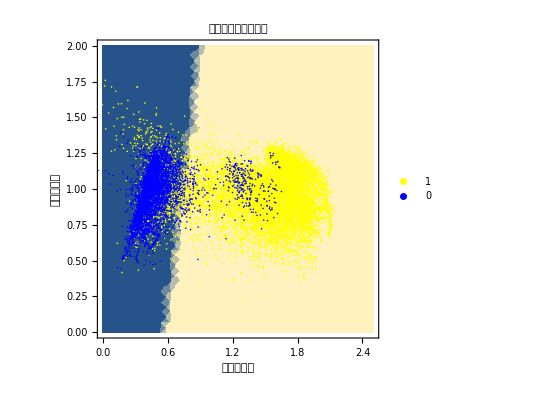

```mathematica
linearplot=Show[dens,ListPlot[{point1,point2},PlotStyle->{Yellow,Blue,Red},PlotLegends->{1,0}],PlotLabel->"线性核下的训练结果",FrameLabel->{"第一主向量","第二主向量"}]
```

```mathematica
Export[path<>"//线性核下的分类结果.jpg",linearplot2];
```

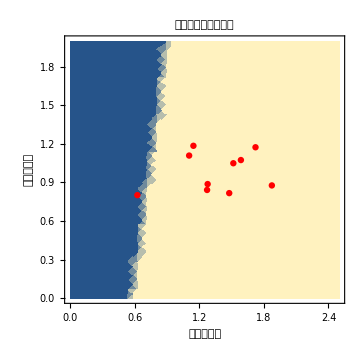

```mathematica
linearplot2=Show[dens,plot,PlotLabel->"线性核下的训练结果",FrameLabel->{"第一主向量","第二主向量"}]
```

```mathematica
result=model2/@transformedtest[[1;;10]]
```

{1.,1.,1.,1.,0.,1.,1.,1.,1.,1.}

```mathematica
modelRBF=Classify[asso2,Method->{"SupportVectorMachine","KernelType"->"RadialBasisFunction"}];
```

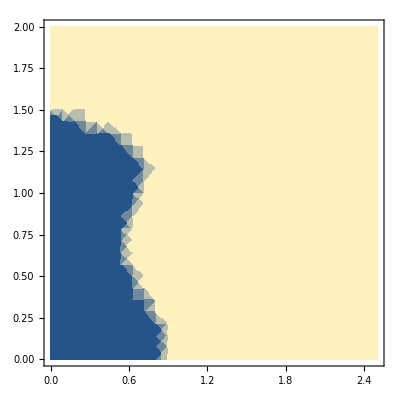

```mathematica
dens2=DensityPlot[modelRBF[{x,y}],{x,0,2.5},{y,0,2}]
```

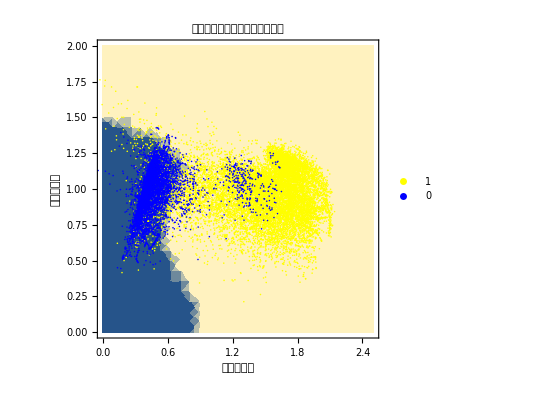

```mathematica
RBFplot=Show[dens2,ListPlot[{point1,point2},PlotStyle->{Yellow,Blue,Red},PlotLegends->{1,0}],PlotLabel->"高斯径向基函数核下的训练结果",FrameLabel->{"第一主向量","第二主向量"}]
```

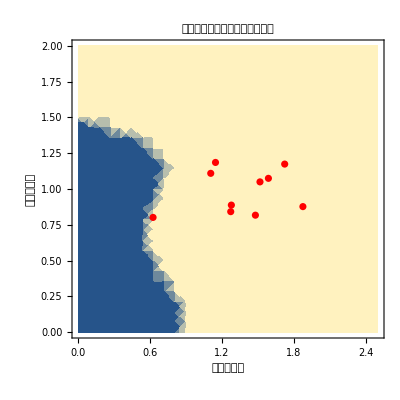

```mathematica
RBFplot2=Show[dens2,plot,PlotLabel->"高斯径向基函数核下的训练结果",FrameLabel->{"第一主向量","第二主向量"}]
```

```mathematica
Export[path<>"//RBF核分类结果.jpg",RBFplot2];
```

```mathematica
modelRBF/@transformedtest[[1;;10]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
model3=Classify[asso2,Method->{"SupportVectorMachine","KernelType"->"Sigmoid"}];
```

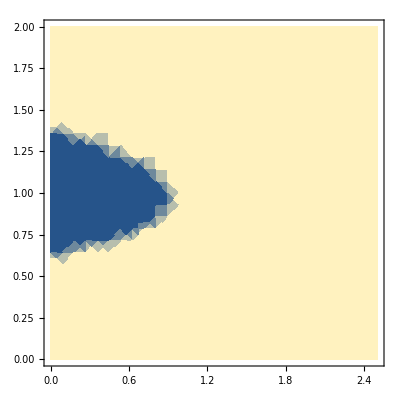

```mathematica
dens3=DensityPlot[model3[{x,y}],{x,0,2.5},{y,0,2}]
```

```mathematica
modelPolinomial=Classify[asso2,Method->{"SupportVectorMachine","KernelType"->"Polynomial"}];
```

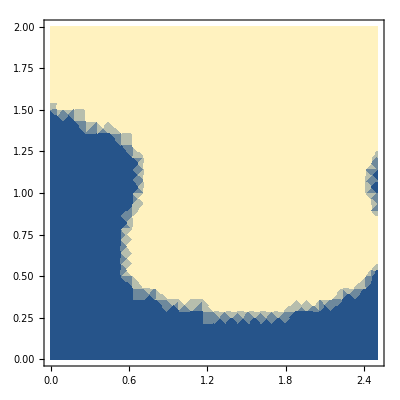

```mathematica
densPolinomial=DensityPlot[modelPolinomial[{x,y}],{x,0,2.5},{y,0,2}]
```

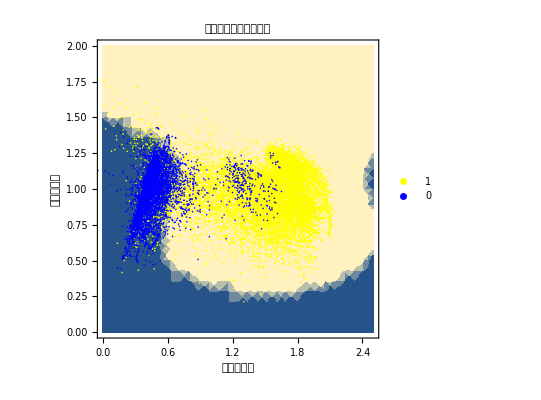

```mathematica
polynomialplot=Show[densPolinomial,ListPlot[{point1,point2},PlotStyle->{Yellow,Blue,Red},PlotLegends->{1,0}],PlotLabel->"多项式核下的训练结果",FrameLabel->{"第一主向量","第二主向量"}]
```

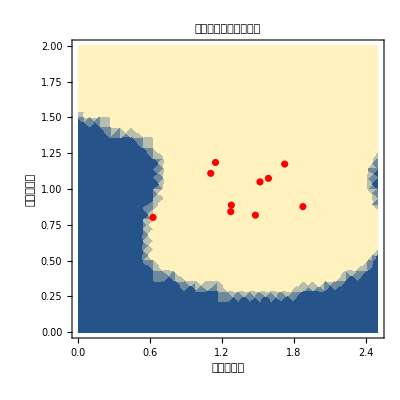

```mathematica
polynomialplot2=Show[densPolinomial,plot,PlotLabel->"多项式核下的训练结果",FrameLabel->{"第一主向量","第二主向量"}]
```

```mathematica
modelPolinomial/@transformedtest[[1;;10]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Export[path<>"//多项式核分类结果.jpg",polynomialplot2];
```

```mathematica
Classify[asso]
```

ClassifierFunction[…]

```mathematica
Classify[asso2]
```

ClassifierFunction[…]

```mathematica
classWith7=Out[82];
```

```mathematica
classWith2=Out[83];
```

```mathematica
Information[classWith2]
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,0.1.
Accuracy | (92.80.6) %
Method | NaiveBayes
Single evaluation time | 6.53 ms/example
Batch evaluation speed | 17.5 examples/ms
Loss | 0.223 ± 0.013
Model memory | 212. kB
Training examples used | 20000 examples
Training time | 15.7 s
 |

```mathematica
classWith7//Information
```

Classifier information
Data type | NumericalVector (length: 7)
Classes | ,,0.1.
Accuracy | (95.11.6) %
Method | NearestNeighbors
Single evaluation time | 4.05 ms/example
Batch evaluation speed | 4.97 examples/ms
Loss | 0.148 ± 0.025
Model memory | 1.33 MB
Training examples used | 19999 examples
Training time | 23.7 s
 |

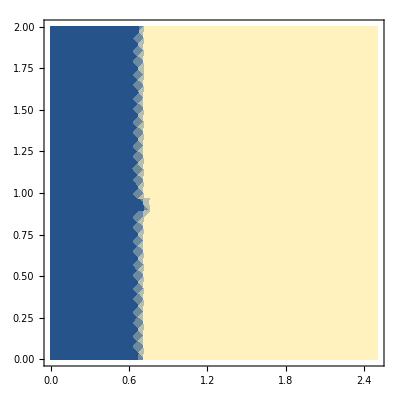

```mathematica
dens4=DensityPlot[classWith2[{x,y}],{x,0,2.5},{y,0,2}]
```

```mathematica
model2//Information
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,0.1.
Accuracy | (91.21.3) %
Method | SupportVectorMachine
Single evaluation time | 5.69 ms/example
Batch evaluation speed | 8.47 examples/ms
Loss | 0.256 ± 0.039
Model memory | 1.02 MB
Training examples used | 20000 examples
Training time | 52.3 s
 |

```mathematica
model2//Information
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,0.1.
Accuracy | (91.21.3) %
Method | SupportVectorMachine
Single evaluation time | 8.62 ms/example
Batch evaluation speed | 6.8 examples/ms
Loss | 0.256 ± 0.039
Model memory | 1.02 MB
Training examples used | 20000 examples
Training time | 52.3 s
 |